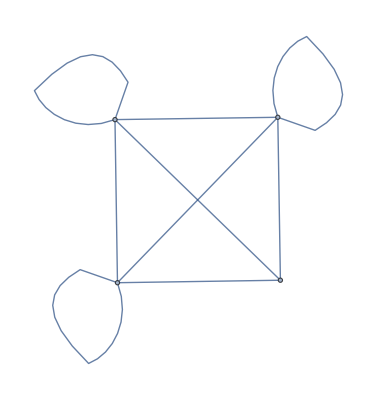

```mathematica
(*SetDirectory["~/Documents/UNH/Research/code/OTimes/graph_18b/polynomial_18b"];*)
gammaAdj = { {0,1,1,1},{1,1,1,1},{1,1,1,1}, {1,1,1,1} };
AdjacencyGraph[ gammaAdj] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo];
gammaSym = { 
{0,aa,bb,cc},
{dd,ee,ff,gg},
{hh,ii,jj,kk}, 
{ll,mm,nn,oo} 
};
q=Exp[2*Pi*I/42]; (* 2*Pi*I/(3*(4+ level)) *)
delta = AlgebraicNumber"3.79"AlgebraicNumber[Root[1+8 #1+8 #1^2-6 #1^3-6 #1^4+#1^5+#1^6&,6],{0,6,4,-5,-1,1}]3.7912878474779195;
quan[n_,q_]:=(q^n-q^-n)/(q-q^-1)
inDeg[x_]:=360*Arg[x]/(2Pi)

Hom3to3 = GetHomBasisList[gammaSym, 3,3];
dim3to3 = Length[Hom3to3];
Hom2to4 = GetHomBasisList[gammaSym, 2,4];
dim2to4 = Length[Hom2to4];
Hom4to2 = GetHomBasisList[gammaSym, 4,2];
dim4to2 = Length[Hom4to2];
Hom4to4 = GetHomBasisList[gammaSym, 4,4];
dim4to4 = Length[Hom4to4];
Hom4to1 = GetHomBasisList[gammaSym, 4,1];
dim4to1 = Length[Hom4to1];
Hom4to0 = GetHomBasisList[gammaSym, 4,0];
dim4to0 = Length[Hom4to0];
Hom0to4 = GetHomBasisList[gammaSym, 0,4];
dim0to4 = Length[Hom0to4];
Hom2to3 = GetHomBasisList[gammaSym, 2,3];
dim2to3 = Length[Hom2to3];
Hom2to2 = GetHomBasisList[gammaSym,2,2];
dim2to2 = Length[Hom2to2];
Hom2to1 = GetHomBasisList[gammaSym,2,1];
dim2to1 = Length[Hom2to1];
Hom2to0 = GetHomBasisList[gammaSym,2,0];
dim2to0 = Length[Hom2to0];
Hom1to2 = GetHomBasisList[gammaSym,1,2];
dim1to2 = Length[Hom1to2];
Hom1to1 = GetHomBasisList[gammaSym,1,1];
dim1to1 = Length[Hom1to1];
Hom1to0 = GetHomBasisList[gammaSym,1,0];
dim1to0 = Length[Hom1to0];
Hom0to1 = GetHomBasisList[gammaSym,0,1];
dim0to1 = Length[Hom0to1];
Hom0to0 = GetHomBasisList[gammaSym,0,0];
dim0to0 = Length[Hom0to0];
Hom0to2 = GetHomBasisList[gammaSym, 0,2];
dim0to2 = Length[Hom0to2];

Stick = GenerateStick[gammaAdj, gammaSym];
DoubleStick = InTermsOf[Tens[{Stick, Stick}], Hom2to2];
```